```mathematica
(*Mathematica*)
```

```mathematica
Clear[s,w]
```

```mathematica
(*First so(5)*)
s[1]={{0,1,0,0,0},
           {1,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[2]={{0,0,1,0,0},
           {0,0,0,0,0},
          {1,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[3]={{0,0,0,1,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0},
{0,0,0,0,0}};
s[4]={{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{1,0,0,0,0}};
s[5]={{0,0,0,0,0},
{0,0,1,0,0},
{0,1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[10]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,1},
        { 0,0,0,1,0}};
s[9]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,1,0,0}};
s[8]={{0,0,0,0,0},
{0,0,0,0,1},
{0,0,0,0,0},
{0,0,0,0,0},
{0,1,0,0,0}};
s[7]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,1,0},
{0,0,1,0,0},
{0,0,0,0,0}};
s[6]={{0,0,0,0,0},
{0,0,0,1,0},
{0,0,0,0,0},
{0,1,0,0,0},
{0,0,0,0,0}};
(* second so(5) *)
s[11]={{0,I,0,0,0},
           {-I,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,0}};
s[12]={{0,0,-I,0,0},
           {0,0,0,0,0},
          {I,0,0,0,0},
          {0,0,0,0,0},
         {0,0,0,0,0}};
s[13]={{0,0,0,I,0},
{0,0,0,0,0},
{0,0,0,0,0},
{-I,0,0,0,0},
{0,0,0,0,0}};
s[14]={{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{I,0,0,0,0}};
s[15]={{0,0,0,0,0},
{0,0,I,0,0},
{0,-I,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[20]={{0,0,0,0,0},
           {0,0,0,0,0},
           {0,0,0,0,0},
          {0,0,0,0,I},
        { 0,0,0,-I,0}};
s[19]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,-I},
{0,0,0,0,0},
{0,0,I,0,0}};
s[18]={{0,0,0,0,0},
{0,0,0,0,I},
{0,0,0,0,0},
{0,0,0,0,0},
{0,-I,0,0,0}};
s[17]={{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,I,0},
{0,0,-I,0,0},
{0,0,0,0,0}};
s[16]={{0,0,0,0,0},
{0,0,0,-I,0},
{0,0,0,0,0},
{0,I,0,0,0},
{0,0,0,0,0}};
(* DIAGONAL four: n-1 matrices*)
(* zero trace with normalization Sqrt[n*(n-1)/2]*)
s[21]={{1,0,0,0,0},
{0,-1,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0},
{0,0,0,0,0}};
s[22]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,-2,0,0},
{0,0,0,0,0},
{0,0,0,0,-1}}/Sqrt[7/2];
s[23]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,-3,0},
{0,0,0,0,0}}/Sqrt[6];
s[24]={{1,0,0,0,0},
{0,1,0,0,0},
{0,0,1,0,0},
{0,0,0,1,0},
{0,0,0,0,-4}}/Sqrt[10];
s[25]=IdentityMatrix[5];
```

```mathematica
(*U(1)*SU(5):deSitter groupm sum*)
```

```mathematica
gs=N[Sum[s[i],{i,25}]]
```

{{3.259,1.+1. ⅈ,1.-1. ⅈ,1.+1. ⅈ,1.-1. ⅈ},{1.-1. ⅈ,1.259,1.+1. ⅈ,1.-1. ⅈ,1.+1. ⅈ},{1.+1. ⅈ,1.-1. ⅈ,0.655431,1.+1. ⅈ,1.-1. ⅈ},{1.-1. ⅈ,1.+1. ⅈ,1.-1. ⅈ,0.0914829,1.+1. ⅈ},{1.+1. ⅈ,1.-1. ⅈ,1.+1. ⅈ,1.-1. ⅈ,-0.799434}}

```mathematica
(*trace normalized to 10*)
```

```mathematica
ca0=gs.Transpose[gs]/(13.283201839915929/10)//Chop
```

{{7.99587,7.91827-1.50566 ⅈ,4.45256+1.96005 ⅈ,4.02801-2.3846 ⅈ,6.36862+3.05531 ⅈ},{7.91827-1.50566 ⅈ,1.19329,5.95822-0.454384 ⅈ,2.52234+0.878941 ⅈ,1.85164-1.54965 ⅈ},{4.45256+1.96005 ⅈ,5.95822-0.454384 ⅈ,0.323408,5.07928-0.424557 ⅈ,1.39725+1.09527 ⅈ},{4.02801-2.3846 ⅈ,2.52234+0.878941 ⅈ,5.07928-0.424557 ⅈ,0.00630053,3.98402-0.670709 ⅈ},{6.36862+3.05531 ⅈ,1.85164-1.54965 ⅈ,1.39725+1.09527 ⅈ,3.98402-0.670709 ⅈ,0.481129}}

```mathematica
TableForm[ca0]
```

7.99587 | 7.91827-1.50566 ⅈ | 4.45256+1.96005 ⅈ | 4.02801-2.3846 ⅈ | 6.36862+3.05531 ⅈ
7.91827-1.50566 ⅈ | 1.19329 | 5.95822-0.454384 ⅈ | 2.52234+0.878941 ⅈ | 1.85164-1.54965 ⅈ
4.45256+1.96005 ⅈ | 5.95822-0.454384 ⅈ | 0.323408 | 5.07928-0.424557 ⅈ | 1.39725+1.09527 ⅈ
4.02801-2.3846 ⅈ | 2.52234+0.878941 ⅈ | 5.07928-0.424557 ⅈ | 0.00630053 | 3.98402-0.670709 ⅈ
6.36862+3.05531 ⅈ | 1.85164-1.54965 ⅈ | 1.39725+1.09527 ⅈ | 3.98402-0.670709 ⅈ | 0.481129

```mathematica
Det[ca0]//Chop
```

341.985

```mathematica
Tr[ca0]
```

10.

```mathematica
ei=Eigenvalues[ca0]//Chop
```

{20.8024,-5.30072-3.05243 ⅈ,-5.30072+3.05243 ⅈ,-0.100465+0.655206 ⅈ,-0.100465-0.655206 ⅈ}

```mathematica
Abs[ei]
```

{20.8024,6.11678,6.11678,0.662864,0.662864}

```mathematica
Apply[Plus,{20.802366352448942,6.116777214608377,6.116777214608372,0.6628636481297079,0.6628636481297077}]
```

34.3616

```mathematica
34.3616480779251-Det[ca0]/10//Chop
```

0.163194

```mathematica
ga=ComplexListPlot[ei,PlotStyle->Red,ImageSize->Full];
```

```mathematica
Apply[Plus,ei]//Chop
```

10.

```mathematica
p[x_]=CharacteristicPolynomial[ca0,x]//Chop
```

341.985+236.849 x+819.596 x^2+184.73 x^3+10. x^4-x^5

```mathematica
r=N[Exp[2*Pi*I/5]]
```

0.309017+0.951057 ⅈ

```mathematica
rc=-Conjugate[r]
```

-0.309017+0.951057 ⅈ

```mathematica
ca0c=Table[If[i>j,ca0[[i,j]]*r,If[j>i,ca0[[i,j]]*rc,If[i==j,ca0[[i,j]],Nothing]]],{i,5},{j,5}]
```

{{7.99587,-1.01491+7.996 ⅈ,-3.24003+3.62895 ⅈ,1.02317+4.56774 ⅈ,-4.87379+5.11277 ⅈ},{3.87885+7.06545 ⅈ,1.19329,-1.40905+5.80702 ⅈ,-1.61537+2.12728 ⅈ,0.901618+2.23988 ⅈ},{-0.488196+4.84033 ⅈ,2.27334+5.5262 ⅈ,0.323408,-1.16581+4.96188 ⅈ,-1.47343+0.990409 ⅈ},{3.51261+3.09398 ⅈ,-0.0564756+2.6705 ⅈ,1.97336+4.69949 ⅈ,0.00630053,-0.593246+3.99629 ⅈ},{-0.937763+7.00106 ⅈ,2.04599+1.28214 ⅈ,-0.609886+1.66732 ⅈ,1.86901+3.58176 ⅈ,0.481129}}

```mathematica
Det[ca0c]//Chop
```

-1910.95-7176.79 ⅈ

```mathematica
Tr[ca0c]
```

10.

```mathematica
eic=Eigenvalues[ca0c]//Chop
```

{2.71161+17.0152 ⅈ,7.3549-7.92984 ⅈ,-2.44259-6.44628 ⅈ,1.27926-3.65301 ⅈ,1.09682+1.01394 ⅈ}

```mathematica
Apply[Plus,{2.7116103979455843+17.015181181138612 ⅈ,7.354896232683963-7.92983671096517 ⅈ,-2.4425911365814095-6.446275924641314 ⅈ,1.2792596854949154-3.6530112604747327 ⅈ,1.0968248204569613+1.0139427149426192 ⅈ}]//Chop
```

10.

```mathematica
Apply[Plus,Abs[{2.7116103979455843+17.015181181138612 ⅈ,7.354896232683963-7.92983671096517 ⅈ,-2.4425911365814095-6.446275924641314 ⅈ,1.2792596854949154-3.6530112604747327 ⅈ,1.0968248204569613+1.0139427149426192 ⅈ}]]//Chop
```

40.3032

```mathematica
gb=ComplexListPlot[eic,PlotStyle->Blue];
```

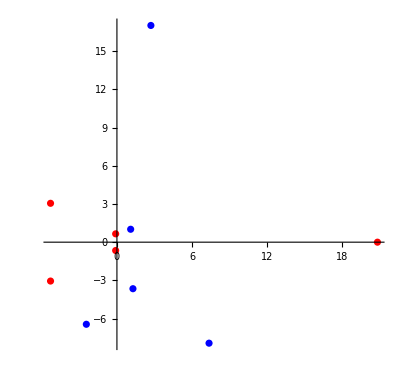

```mathematica
Show[{ga,gb},PlotRange->All]
```

```mathematica
q[x_]=CharacteristicPolynomial[ca0c,x]//Chop
```

(-1910.95-7176.79 ⅈ)+(1604.82+4165.66 ⅈ) x+(828.329-1717.72 ⅈ) x^2-219.036 x^3+10. x^4-x^5

```mathematica
ph[x_]=x^2*q[x]/p[x]
```

(x^2 ((-1910.95-7176.79 ⅈ)+(1604.82+4165.66 ⅈ) x+(828.329-1717.72 ⅈ) x^2-219.036 x^3+10. x^4-x^5))/(341.985+236.849 x+819.596 x^2+184.73 x^3+10. x^4-x^5)

```mathematica
g1=JuliaSetPlot[ph[x]/N[4],x,ColorFunction->Hue,ImageSize->2000,AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality",Frame->False,Axes->False];
```

```mathematica
g2=ListPlot[JuliaSetPoints[ph[x]/N[4],x],ImageSize->2000,PlotStyle->{PointSize[0.001]},ColorFunction->Hue,PlotRange->All,AspectRatio->1];
```

```mathematica
Export["Julia_Cartan_SU5_Hermanrings_scale4_both.jpg",{g1,g2}]
```

Julia_Cartan_SU5_Hermanrings_scale4_both.jpg

```mathematica
(*end*)
```